```mathematica
basicRays={{0,0,1},{1,-1,0},{1,1,0},{1,√2,0},{-1,0,√2},{√2,1,1},{√2,-1,-1},{√2,1,-1}};
```

```mathematica
Union@@Permutations/@basicRays
```

{{-1,-1,√2},{-1,0,1},{-1,0,√2},{-1,1,0},{-1,1,√2},{-1,√2,-1},{-1,√2,0},{-1,√2,1},{0,-1,1},{0,-1,√2},{0,0,1},{0,1,-1},{0,1,0},{0,1,1},{0,1,√2},{0,√2,-1},{0,√2,1},{1,-1,0},{1,-1,√2},{1,0,-1},{1,0,0},{1,0,1},{1,0,√2},{1,1,0},{1,1,√2},{1,√2,-1},{1,√2,0},{1,√2,1},{√2,-1,-1},{√2,-1,0},{√2,-1,1},{√2,0,-1},{√2,0,1},{√2,1,-1},{√2,1,0},{√2,1,1}}

```mathematica
thirtyThreeRays={{-1,-1,√2},{-1,0,√2},{-1,1,√2},{-1,√2,-1},{-1,√2,0},{-1,√2,1},{0,-1,√2},{0,0,1},{0,1,-1},{0,1,0},{0,1,1},{0,1,√2},{0,√2,-1},{0,√2,1},{1,-1,0},{1,-1,√2},{1,0,-1},{1,0,0},{1,0,1},{1,0,√2},{1,1,0},{1,1,√2},{1,√2,-1},{1,√2,0},{1,√2,1},{√2,-1,-1},{√2,-1,0},{√2,-1,1},{√2,0,-1},{√2,0,1},{√2,1,-1},{√2,1,0},{√2,1,1}};
```

```mathematica
Length@thirtyThreeRays
```

33

```mathematica
orthogonalityGraph[statelist_]:=AdjacencyGraph[Outer[Dot,statelist,statelist,1]/.{0->1,x_/;x≠0->0}]
```

```mathematica
vectorToNumber[vector_]:=Position[Abs[Conjugate[Normalize[vector]].#]&/@(Normalize/@thirtyThreeRays),1][[1,1]]
```

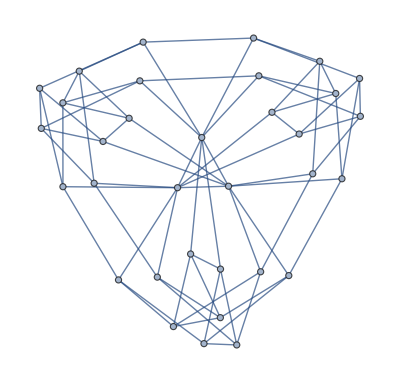

```mathematica
rayGraph=orthogonalityGraph[thirtyThreeRays]
```

```mathematica
Length@FindIndependentVertexSet[rayGraph][[1]]
```

12

```mathematica
contexts=Sort[Sort/@FindClique[rayGraph,{3},All]]
```

{{1,15,22},{2,10,30},{3,16,21},{4,17,25},{5,8,32},{6,19,23},{7,14,18},{8,10,18},{8,15,21},{8,24,27},{9,11,18},{9,26,33},{10,17,19},{10,20,29},{11,28,31},{12,13,18}}

```mathematica
independentSets=Union@@(FindIndependentVertexSet[{rayGraph,#},Infinity,All]&/@{8,15,21,24,2,33,26,31});
```

```mathematica
independentSets
```

```mathematica
Length@independentSets
```

```mathematica
Length/@independentSets
```

```mathematica
Select[independentSets,Length@#==12&]
```

{{1,2,4,5,7,11,13,19,21,26,27,29},{1,2,7,9,13,17,21,23,24,29,31,32},{2,3,5,6,11,12,14,15,17,26,27,29},{2,3,9,12,14,15,19,24,25,29,31,32},{4,5,7,9,13,15,16,19,20,27,28,30},{5,6,9,12,14,17,20,21,22,27,28,30},{7,11,13,15,16,17,20,23,24,30,32,33},{11,12,14,19,20,21,22,24,25,30,32,33}}

```mathematica
unsolvedContexts[contexts_,oneAssignment_]:=Select[contexts/.Thread[Unevaluated[oneAssignment->Nothing]],Length[#]==Max[Length/@contexts]&]
```

```mathematica
unsolvedContexts[contexts,{1,2,4,5,7,11,13,19,21,26,27,29}]
```

{{8,10,18}}

```mathematica
unsolvedContexts[contexts,Select[independentSets,Length@#==11&][[1]]]
```

{{8,10,18},{8,15,21},{12,13,18}}

```mathematica
variablesInQuestion[contexts_]:=Union@@contexts
```

```mathematica
recursiveSolubleWith[contexts_,n_,minimum_:0]:=Or@@(recursiveSolubleWith[unsolvedContexts[contexts,#],n-1,#]&/@Select[variablesInQuestion@contexts,#>minimum&]);
recursiveSolubleWith[contexts_,0,minimum_:0]:=contexts=={}
```

```mathematica
Parallelize[recursiveSolubleWith[unsolvedContexts[contexts,{#}],5]&/@(Select[independentSets,Length@#==12&])]&/@{8,15,21,24,2,33,26,31}
```